```mathematica
a
```

original data

```mathematica
10^4Round[#,10^-4]&/@{{0.1829954,0.080675},{0.1847784982719759,0.07252460390683695},{0.18217031510142748,0.06534561637866265},{0.17596979714500374,0.059081174906085644},{0.16697589105935387,0.0536744169797145},{0.15598754350112695,0.049068480090157775},{0.14380370112697216,0.04520650172802404},{0.13122331059353864,0.04203161938392186},{0.11904531855747556,0.0394869705484598},{0.10806867167543201,0.037515692712246425},{0.09909231660405707,0.03606092336589031},{0.09291519999999999,0.0350658},{0.0929152,0.033934473779113454},{0.10260248685199098,0.030019441622839968},{0.11297373944402705,0.026402584222389176},{0.12386195492111193,0.022894781667918855},{0.1351001304282494,0.01973098782870022},{0.14652126311044328,0.01714615657400451},{0.15795835011269715,0.01537524177310293},{0.169244388580015,0.01465319729526672},{0.18021237565740042,0.015214977009767093},{0.19069530848985725,0.017295534785875283},{0.20052618422238916,0.021129824492862513},{0.20953799999999995,0.026952800000000002},{0.21210008835462055,0.025085907888805405},{0.2125433382419233,0.02267816558978212},{0.2112481541697971,0.01987759233658903},{0.20859494064613074,0.016832207362885043},{0.20496410217881286,0.01369002990232907},{0.2007360432757325,0.01059907918858001},{0.1962911684447783,0.007707374455296766},{0.1920098821938392,0.005162934936138233},{0.18827258903080393,0.003113779864763327},{0.1854596934635612,0.0017079284748309457},{0.1839516,0.0010933999999999883},{0.17883091645379412,0.00012073132982719807},{0.1737303398948159,-0.00043446175807663345},{0.1686528996243426,-0.0006017780616078129},{0.16360162494365132,-0.0004108163786626587},{0.15857954515401954,0.0001088244928625103},{0.15358968955672425,0.0009275457550713761},{0.14863508745304277,0.002015748610067618},{0.14371876814425236,0.0033438342599549243},{0.1388437609316303,0.004882203906836966},{0.1340130951164537,0.006601258752817435},{0.12922979999999992,0.008471400000000002},{0.12466071329827194,0.010394841172051089},{0.12013538737791132,0.012420420285499625},{0.11564919624342596,0.014535729827197592},{0.11119751389932378,0.016728362283996993},{0.10677571435011267,0.018985910142749807},{0.1023791716003005,0.021295965890308036},{0.09800325965439517,0.02364612201352366},{0.09364335251690456,0.026023970999248674},{0.08929482419233656,0.02841710533433508},{0.08495304868519908,0.030813117505634847},{0.08061339999999999,0.03319959999999998},{0.07637008204357623,0.03405250503380916},{0.07201055882794888,0.034505775807663404},{0.0675569126972201,0.034645173102930124},{0.06303122599549207,0.0345564577009767},{0.05845558106686699,0.03432539038317054},{0.05385206025544699,0.03403773193087903},{0.0492427459053343,0.033779243125469566},{0.044649720360631064,0.03363568474830953},{0.040095065965439464,0.03369281758076634},{0.03560086506386172,0.03403640240420736},{0.031189199999999945,0.03475219999999999},{0.03544959774605558,0.03756568249436513},{0.03994360510894063,0.03946622193839218},{0.044630825093914334,0.04058879263711495},{0.04947086070623589,0.041068368895567225},{0.05442331495116453,0.04103992501878286},{0.059447790833959395,0.04063843531179564},{0.06450389135987977,0.03999887407963936},{0.0695512195341848,0.03925621562734786},{0.07454937836213374,0.038545434259954915},{0.07945797084898573,0.038001504282494346},{0.08423660000000002,0.03775939999999999},{0.09030754169797144,0.038702153268219366},{0.09641984598046581,0.0396196939143501},{0.102556422539444,0.04054852501878286},{0.108700181066867,0.04152514966190834},{0.11483403125469568,0.042586070924117196},{0.12094088279489104,0.04376779188580014},{0.12700364537941392,0.04510681562734785},{0.13300522870022533,0.04663964522915101},{0.1389285424492862,0.04840278377160029},{0.1447564963185574,0.05043273433508639},{0.15047199999999994,0.052765999999999987},{0.15314431600300527,0.05399127137490608},{0.15577188670172798,0.055289328024042066},{0.15835182794891056,0.05666277009767092},{0.16088125559729524,0.05811419774605559},{0.16335728549962428,0.059646211119459044},{0.1657770335086401,0.061261410368144247},{0.16813761547708483,0.06296239564237416},{0.1704361472577009,0.06475176709241173},{0.1726697447032306,0.06663212486851992},{0.17483552366641614,0.06860606912096169},{0.1769305999999999,0.07067620000000002},{0.17584217099924862,0.0724872320060105},{0.17452219609316302,0.07405750398196843},{0.17300438888054093,0.07541512531930877},{0.17132246296018028,0.07658820540946655},{0.169510131930879,0.07760485364387677},{0.167601109391435,0.07849317941397445},{0.1656291089406461,0.07928129211119456},{0.16362784417731027,0.07999730112697218},{0.1616310287002254,0.08066931585274227},{0.15967237610818932,0.08132544567993986},{0.15778559999999997,0.08199379999999998},{0.15194989406461304,0.08397647978963184},{0.1460205574755822,0.08564129120961682},{0.1400117711495116,0.08701344688204357},{0.13393771600300525,0.08811815942900074},{0.12781257295266718,0.088980641472577},{0.12165052291510144,0.08962610563486101},{0.11546574680691207,0.09007976453794139},{0.1092724255447032,0.09036683080390684},{0.1030847400450789,0.09051251705484599},{0.09691687122464311,0.09054203591284748},{0.09078300000000002,0.09048060000000001},{0.08605459519158526,0.09051127272727272},{0.08047936814425243,0.09067162479338842},{0.07428868174305031,0.09085912066115702},{0.06771389887302777,0.09097122479338843},{0.060986382419233647,0.09090540165289256},{0.05433749526671674,0.09055911570247932},{0.047998600300525905,0.08982983140495866},{0.04220106040570999,0.08861501322314048},{0.03717623846731779,0.0868121256198347},{0.03315549737039819,0.08431863305785123},{0.03037019999999999,0.08103199999999999},{0.029443484147257695,0.075772784823441},{0.028687008715251684,0.07049333643876783},{0.02807906371149511,0.06519667783621337},{0.02759793914350112,0.059885832006010505},{0.027221925018782858,0.05456382193839218},{0.02692931134485348,0.04923367062359128},{0.02669838812922614,0.043898401051840716},{0.026507445379413963,0.038561036213373395},{0.02633477310293012,0.033224599098422236},{0.02615866130728775,0.027892112697220136},{0.02595739999999999,0.0225666},{0.02593725304282493,0.02075267438016528},{0.02597512351615326,0.018571161983471064},{0.02602031480090157,0.016135914049586766},{0.02602213027798646,0.013560781818181806},{0.02592987332832456,0.010959616528925608},{0.025692847332832443,0.008446269421487596},{0.025260355672426738,0.0061345917355371815},{0.024581701728024027,0.0041384347107437935},{0.02360618888054093,0.0025716495867768494},{0.022283120510894056,0.0015480876033057713},{0.020561799999999984,0.0011815999999999897},{0.01834097610818932,0.0013378057099924785},{0.01650220390683696,0.0017889580766341014},{0.015007396243425992,0.0025088599549211036},{0.013818465965439506,0.003471314199849729},{0.012897325920360624,0.004650123666416221},{0.012205888955672421,0.006019091209616821},{0.011706067918857997,0.0075520196844477755},{0.011359775657400444,0.009222711945905326},{0.011128925018782862,0.011004970848985718},{0.010975428850488349,0.01287259924868519},{0.010861199999999996,0.014799399999999992},{0.010390844177310286,0.020940816078136727},{0.009723110443275722,0.027405098873027788},{0.00899363576258451,0.03409275477084897},{0.008338057099924865,0.040904290157776094},{0.007892011419984963,0.047740211419984954},{0.007791135687453036,0.05450102494365137},{0.008171066867017265,0.061087237114951135},{0.00916744192336588,0.06739935432006008},{0.010915897821187069,0.07333788294515399},{0.013552071525169034,0.07880332937640869},{0.01721159999999999,0.08369619999999997},{0.013885071675431994,0.08321494815927871},{0.01056804778362132,0.08267413899323814},{0.007261424492862499,0.08207426476333582},{0.003966097971450025,0.08141581773102928},{0.0006829643876784291,0.08069929015777608},{-0.0025870800901577834,0.07992517430503379},{-0.005843139293764093,0.07909396243425995},{-0.00908431705484599,0.0782061468069121},{-0.01230971720510895,0.07726221968444778},{-0.015518443576258454,0.07626267332832457},{-0.018709600000000003,0.075208},{-0.01976051404958678,0.07475520781367392},{-0.021211157024793394,0.07402645259203604},{-0.022956216528925624,0.07313342088655146},{-0.024890380165289258,0.0721877992486852},{-0.02690833553719009,0.07130127422990232},{-0.02890477024793389,0.0705855323816679},{-0.030774371900826446,0.070152260255447},{-0.032411828099173555,0.0701131444027047},{-0.03371182644628099,0.07057987137490607},{-0.03456905454545455,0.07166412772351613},{-0.0348782,0.07347759999999996},{-0.03469251119459053,0.07476564312546954},{-0.03417215401953419,0.0759602259954921},{-0.03337219233658903,0.07706611975957924},{-0.032347690007513155,0.07808809556724264},{-0.031153710894064615,0.07903092456799399},{-0.029845318858001506,0.07989937791134484},{-0.028477577761081896,0.08069822674680689},{-0.027105551465063868,0.08143224222389181},{-0.02578430383170549,0.08210619549211119},{-0.024568898722764843,0.0827248577009767},{-0.023514400000000005,0.083293},{-0.017791798497370403,0.08631914891059352},{-0.011931515251690464,0.08898477310293011},{-0.005950123065364393,0.09132338422238916},{0.000135805259203604,0.09336849391435008},{0.006309696919609309,0.09515361382419231},{0.01255497911344852,0.09671225559729524},{0.018855079038317044,0.0980779308790383},{0.025193423891810656,0.09928415131480088},{0.03155344087152515,0.10036442854996241},{0.037918557175056315,0.1013522742299023},{0.044272199999999984,0.10228119999999996},{0.05028200661157023,0.10309940165289254},{0.05629056363636362,0.10382575867768593},{0.062299467768595025,0.10445777190082642},{0.06831031570247932,0.1049929421487603},{0.07432470413223138,0.10542877024793386},{0.0803442297520661,0.10576275702479336},{0.08637048925619834,0.1059924033057851},{0.09240507933884295,0.10611520991735533},{0.09844959669421485,0.10612867768595036},{0.10450563801652889,0.1060303074380165},{0.11057479999999996,0.10581759999999994},{0.1165259349361382,0.10550253057851237},{0.12333561172051086,0.1049969685950413},{0.13075982013523663,0.10423301983471073},{0.13855454996243424,0.10314279008264461},{0.1464757909842223,0.10165838512396692},{0.1542795329827197,0.09971191074380165},{0.16172176574004504,0.09723547272727272},{0.16855847903831703,0.09416117685950413},{0.17454566265965435,0.09042112892561982},{0.17943930638617575,0.0859474347107438},{0.18299539999999995,0.0806722}}
```

```mathematica
dragonwickR=(9{.6#[[1]],#[[2]]})&/@(10^-4 {{1830,807},{1848,725},{1822,653},{1760,591},{1670,537},{1560,491},{1438,452},{1312,420},{1190,395},{1081,375},{991,361},{929,351},{929,339},{1026,300},{1130,264},{1239,229},{1351,197},{1465,171},{1580,154},{1692,147},{1802,152},{1907,173},{2005,211},{2095,270},{2121,251},{2125,227},{2112,199},{2086,168},{2050,137},{2007,106},{1963,77},{1920,52},{1883,31},{1855,17},{1840,11},{1788,1},{1737,-4},{1687,-6},{1636,-4},{1586,1},{1536,9},{1486,20},{1437,33},{1388,49},{1340,66},{1292,85},{1247,104},{1201,124},{1156,145},{1112,167},{1068,190},{1024,213},{980,236},{936,260},{893,284},{850,308},{806,332},{764,341},{720,345},{676,346},{630,346},{585,343},{539,340},{492,338},{446,336},{401,337},{356,340},{312,348},{354,376},{399,395},{446,406},{495,411},{544,410},{594,406},{645,400},{696,393},{745,385},{795,380},{842,378},{903,387},{964,396},{1026,405},{1087,415},{1148,426},{1209,438},{1270,451},{1330,466},{1389,484},{1448,504},{1505,528},{1531,540},{1558,553},{1584,567},{1609,581},{1634,596},{1658,613},{1681,630},{1704,648},{1727,666},{1748,686},{1769,707},{1758,725},{1745,741},{1730,754},{1713,766},{1695,776},{1676,785},{1656,793},{1636,800},{1616,807},{1597,813},{1578,820},{1519,840},{1460,856},{1400,870},{1339,881},{1278,890},{1217,896},{1155,901},{1093,904},{1031,905},{969,905},{908,905},{861,905},{805,907},{743,909},{677,910},{610,909},{543,906},{480,898},{422,886},{372,868},{332,843},{304,810},{294,758},{287,705},{281,652},{276,599},{272,546},{269,492},{267,439},{265,386},{263,332},{262,279},{260,226},{259,208},{260,186},{260,161},{260,136},{259,110},{257,84},{253,61},{246,41},{236,26},{223,15},{206,12},{183,13},{165,18},{150,25},{138,35},{129,47},{122,60},{117,76},{114,92},{111,110},{110,129},{109,148},{104,209},{97,274},{90,341},{83,409},{79,477},{78,545},{82,611},{92,674},{109,733},{136,788},{172,837},{139,832},{106,827},{73,821},{40,814},{7,807},{-26,799},{-58,791},{-91,782},{-123,773},{-155,763},{-187,752},{-198,748},{-212,740},{-230,731},{-249,722},{-269,713},{-289,706},{-308,702},{-324,701},{-337,706},{-346,717},{-349,735},{-347,748},{-342,760},{-334,771},{-323,781},{-312,790},{-298,799},{-285,807},{-271,814},{-258,821},{-246,827},{-235,833},{-178,863},{-119,890},{-60,913},{1,934},{63,952},{126,967},{189,981},{252,993},{316,1004},{379,1014},{443,1023},{503,1031},{563,1038},{623,1045},{683,1050},{743,1054},{803,1058},{864,1060},{924,1061},{984,1061},{1045,1060},{1106,1058},{1165,1055},{1233,1050},{1308,1042},{1386,1031},{1465,1017},{1543,997},{1617,972},{1686,942},{1745,904},{1794,859},{1830,807}});
```

```mathematica
Graphics [{Line[{{0,0},{0,1},{1,1},{1,0}}], Line@dragonwickR}]
```

-Graphics-

```mathematica
OverBar[v_]:=v/√(v.v)

rotateAbout[{aa_,bb_,cc_},θ_]:=Module[{a,b,c},
({a,b,c}=OverBar[{aa,bb,cc}];
{{a^2+(b^2+c^2) Cos[θ],a b-a b Cos[θ]+c √(a^2+b^2+c^2) Sin[θ],a c-a c Cos[θ]-b √(a^2+b^2+c^2) Sin[θ]},{a b-a b Cos[θ]-c √(a^2+b^2+c^2) Sin[θ],b^2+(a^2+c^2) Cos[θ],b c-b c Cos[θ]+a √(a^2+b^2+c^2) Sin[θ]},{a c-a c Cos[θ]+b √(a^2+b^2+c^2) Sin[θ],b c-b c Cos[θ]-a √(a^2+b^2+c^2) Sin[θ],c^2+(a^2+b^2) Cos[θ]}})]

moveFromTo[u_,v_,t_ (*in radians*)]:=rotateAbout[u×v,t]

gridOnSphere[nnw_,ssw_,nne_,sse_][{s_ (*0 to 1*),t_ (*0 to 1*)}]:=(
{nw,sw,ne,se}=OverBar[#]&/@{nnw,ssw,nne,sse};

(moveFromTo[
#[[1]],#[[2]],
-s ArcCos[#[[1]].#[[2]]]].#[[1]])&@{moveFromTo[sw,se,-t ArcCos[sw.se]].sw,
moveFromTo[nw,ne,-t ArcCos[nw.ne]].nw})
```

```mathematica
projectFrom[{aa_,bb_,cc_}][uu_]:=Module[{a,b,c,u},
u=OverBar[uu]; {a,b,c}=OverBar[{aa,bb,cc}];If[a==0&&b==0,Drop[u,-1],
Drop[(rotateAbout[-{b,-a,0},ArcCos[c]]).u,-1]]]
```

```mathematica
gridOnSphere[{1,1,1},{1,-1,1},{-1,1,1},{-1,-1,1}][{.5,0}]
```

{0.707107,-5.55112×10^-17,0.707107}

```mathematica
dragonwickROnSphere= gridOnSphere[{1,1,1},{1,-1,1},{-1,1,1},{-1,-1,1}]/@dragonwickR;
```

```mathematica
Graphics3D[
{{Opacity[.8],White, Sphere[{0,0,0},1]},Black, Thick, 
Line@dragonwickROnSphere,Line@(-dragonwickROnSphere)},Lighting->"Neutral",Boxed->False,ViewPoint->100{1,-1.3,4.8}]
```

-Graphics3D-

```mathematica
AbsoluteOptions[%27,{ViewPoint,ViewVertical}]
```

{ViewPoint→{1.3,-2.4,2.},ViewVertical→{0.,0.,1.}}

```mathematica
Show[%27,ViewPoint->{1.3,-2.4,2.}]
```

-Graphics3D-

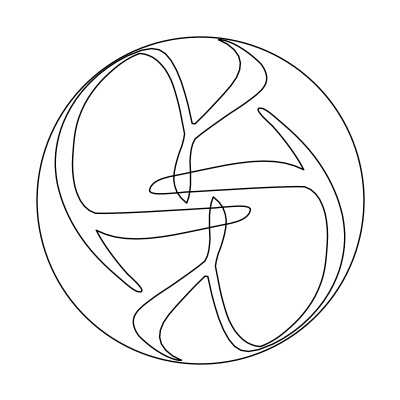

```mathematica
Graphics[{Circle[{0,0},1],Line[projectFrom[100{1,-1.3,2.3}]/@#]&/@
{dragonwickROnSphere,-dragonwickROnSphere}}


]
```

```mathematica
%27//AbsoluteOptions
```

{AlignmentPoint→Center,AspectRatio→1.00787,AutomaticImageSize→False,Axes→False,AxesEdge→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},Boxed→False,BoxRatios→Automatic,BoxStyle→{},ClipPlanes→None,ClipPlanesStyle→Automatic,ColorOutput→Automatic,ContentSelectable→Automatic,ControllerLinking→False,ControllerPath→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction→Identity,Epilog→{},FaceGrids→None,FaceGridsStyle→{},FormatType→TraditionalForm,ImageMargins→0.,ImagePadding→{{0.,0.},{0.,0.}},ImageSize→{360.,362.833},ImageSizeRaw→Automatic,LabelStyle→{},Lighting→Automatic,Method→{CylinderPoints→{40,3},ConePoints→{40,3},SpherePoints→{40,30},TubePoints→{40,2},SplinePoints→7,RotationControl→ArcBall},PlotLabel→None,PlotRange→{{-1.,1.},{-1.,1.},{-1.,1.}},PlotRangePadding→{{0.0416667,0.0416667},{0.0416667,0.0416667},{0.0416667,0.0416667}},PlotRegion→{{0.,1.},{0.,1.}},PreserveImageOptions→Automatic,Prolog→{},RotationAction→Fit,SphericalRegion→Automatic,Ticks→{None,None,None},TicksStyle→{},TouchscreenAutoZoom→False,ViewAngle→Automatic,ViewCenter→Automatic,ViewMatrix→Automatic,ViewPoint→{1.3,-2.4,2.},ViewProjection→Automatic,ViewRange→All,ViewVector→Automatic,ViewVertical→{0.,0.,1.}}